# Maximizing Peak Area (and Peak Height)

## Eric Moyer

June 2013

## Introduction

In order to make the sampled distributions more accurate and avoid missing generated peak parameter values, I will augment the sampled distributions by setting the their maxima and minima to the true maxima and minima.

Peak height is generated by first selecting heights from a known distribution and then dividing them by the highest point in the resulting noiseless spectrum. More complications arise because we are sampling the spectrum to find it's maximum. If the maximum falls between two samples, we will divide by something lower than the maximum, which can lead to maximum heights above 1, despite the fact that the highest point in the sampled spectrum is 1. I deal with these complications in my second calculation of the maximum height. Sampling did not affect the minimum height.

Peak areas are generated by a simple nonlinear formula (that is essentially a scaled product of the parameters). In hindsight (I am writing this introduction after doing the work) it should have been obvious that the maximum area came when you took the maximum of the two main parameters and let P be 1 (since  π>√(π/(log(2))))

The derivatives of the area are {1/2 G (P π+(1-P) √(π/Log[2])),1/2 M (P π+(1-P) √(π/Log[2])),1/2 G M (π-√(π/Log[2]))}. Note that since 0≤P≤1 and all other parameters are strictly positive, the derivative is always positive. So, the area is monotonic in each of the parameters.

I had to recalculate the maximum area when I corrected the maximum height. However, the main work for area is in the first section.

## Final Result

The final result is:

scaled height range:  [ 0.00001604482555427710777509984241, 1.0445079319188184286 ]

area range: [2.93792276627387990798835084182×10^-8,0.073758168890726301241]

## Work

### Calculate max area and max height (wrong)

(Note that the maximum height is incorrect because of sampling. See the section on sampling height for the correct answer.)

Formula for the area of a peak with the given height (M) width at half height (G) and Lorentzianness (P).

```mathematica
area[M_,G_,P_]:=(1/2) M G (P Pi+(1-P) Sqrt[Pi/Log[2]])
```

Take the first derivative with respect to each variable (glad I took Calc 3 :)

```mathematica
D[area[M,G,P],{{M,G,P}}]
```

{1/2 G (P π+(1-P) √(π/Log[2])),1/2 M (P π+(1-P) √(π/Log[2])),1/2 G M (π-√(π/Log[2]))}

Find the zeros of the derivative.

```mathematica
Solve[{1/2 G (P π+(1-P) √(π/Log[2]))==0,1/2 M (P π+(1-P) √(π/Log[2]))==0,1/2 G M (π-√(π/Log[2]))==0},{M,G,P}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{G→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))},{G→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))},{M→0,G→0},{M→0,G→0},{M→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))},{M→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))}}

The only unconstrained optima are where the area is 0. Double check using Mathematica's maximize routine.

```mathematica
Maximize[area[M,G,P],{M,G,P}]
```

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{∞,{M→-∞,G→-1,P→0}}

Now, look at the maxima where the height, width, and lorentzianness are constrained by the values from the original distributions.

Range of Lorentzianness: 0..1

Range of width-at-half-height:  [0.00172017711207981768, 0.0449550522830431884]

Range of height is more complicated because the heights in any spectrum are divided by the height of the highest point in that spectrum. The maximum height is 1 (put all the other peaks as far away as possible and make them as small as possible and their contribution to the largest peak will be negligable.) The minimum is the smallest original height divided by its height plus 6 times the largest original height (put all the peaks at one place and make 6 of them be maximum size.

Unscaled height range: [ 0.000191973000000000013, 1.99409999999999998 ]

min / (6*max + min):

```mathematica
maxOrigHeight =199409999999999998/100000000000000000
```

99704999999999999/50000000000000000

```mathematica
minOrigHeight=191973000000000013/1000000000000000000000
```

191973000000000013/1000000000000000000000

```mathematica
scaledMinHeight=minOrigHeight/(6*maxOrigHeight+minOrigHeight)
```

191973000000000013/11964791972999999880013

```mathematica
N[scaledMinHeight,28]
```

0.00001604482555427710777509984241

So, the range for scaled heights is: [ 0.00001604482555427710777509984241, 1 ]

```mathematica
Maximize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤1,0.00172017711207981768≤G≤0.0449550522830431884},{M,G,P}]
```

{0.070615230997076772,{M→1.,G→0.04495505228304319,P→1.}}

Maximum area is attained by letting all the M,G, and P have their maximum values.

The minimum is probably the same - everything has its minimum value.

```mathematica
Minimize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤1,0.00172017711207981768≤G≤0.0449550522830431884},{M,G,P}]
```

{2.9379227662738799×10^-8,{M→0.00001604482555427711,G→0.001720177112079818,P→0}}

Hmmm. Not quite. Is that round-off error or a real problem. The equation looks like it will be round-off error, but better safe than sorry.

First, calculate the decimals as exact fractions.

```mathematica
minHalfHeightWidth=172017711207981768/100000000000000000000
```

21502213900997721/12500000000000000000

```mathematica
N[minHalfHeightWidth,25]
```

0.00172017711207981768

```mathematica
maxHalfHeightWidth=449550522830431884/10000000000000000000
```

112387630707607971/2500000000000000000

```mathematica
N[maxHalfHeightWidth,25]
```

0.0449550522830431884

Now do the minimize with exact numbers

```mathematica
Minimize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤1,minHalfHeightWidth≤G≤maxHalfHeightWidth},{M,G,P}]
```

{(133156274490846315260057442353883 √(π/Log[2]))/9649025784677419258075000000000000000000,{M→191973000000000013/11964791972999999880013,G→21502213900997721/12500000000000000000,P→0}}

Check that the minimum found for the height is the minimum height

```mathematica
191973000000000013/11964791972999999880013-scaledMinHeight
```

0

Check that the minimum found for the width is the minimum bound for the width

```mathematica
21502213900997721/12500000000000000000-minHalfHeightWidth
```

0

So, everything went to its minimum value to give minimum area.

Finally, redo the maximize with exact numbers to get rid of any residual round-off error. It's not too important, but it's easy to do.

```mathematica
Maximize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤1,minHalfHeightWidth≤G≤maxHalfHeightWidth},{M,G,P}]
```

{(112387630707607971 π)/5000000000000000000,{M→1,G→112387630707607971/2500000000000000000,P→1}}

### Double-check assumption that height contribution of 6 distant small peaks is negligable

Width of most congested spectrum: 0.0260837320427020625

Function for Gauss-Lorentz Peak:

```mathematica
lorentzian[G_,x_,x0_]:=(G^2)/(4(x-x0)^2+G^2)
```

```mathematica
gaussian[G_,x_,x0_]:=Exp[-(x-x0)^2/(2 (G/2 Sqrt[2 Log[2]])^2)]
```

```mathematica
glp[M_,G_,P_,x_,x0_]:=M(P lorentzian[G,x,x0]+(1-P) gaussian[G,x,x0])
```

#### Make sure it looks right

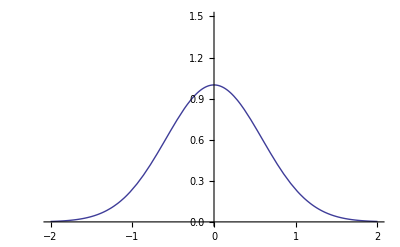

```mathematica
Plot[glp[1,1,0,x,0],{x,-2,2},PlotRange->{0,1.5}]
```

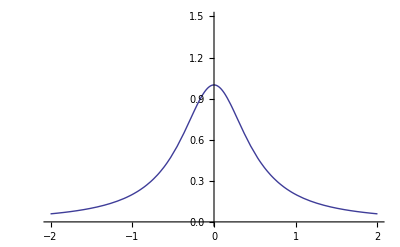

```mathematica
Plot[glp[1,1,1,x,0],{x,-2,2},PlotRange->{0,1.5}]
```

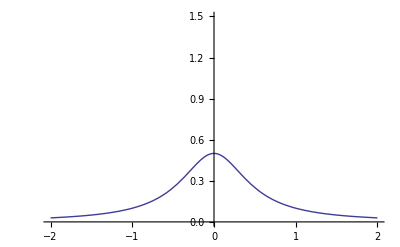

```mathematica
Plot[glp[0.5,1,1,x,0],{x,-2,2},PlotRange->{0,1.5}]
```

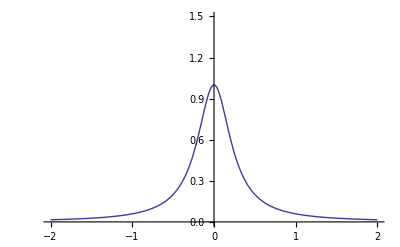

```mathematica
Plot[glp[1,0.5,1,x,0],{x,-2,2},PlotRange->{0,1.5}]
```

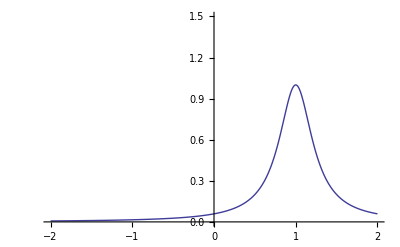

```mathematica
Plot[glp[1,0.5,1,x,1],{x,-2,2},PlotRange->{0,1.5}]
```

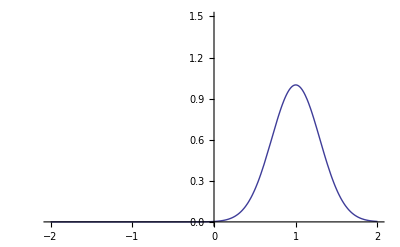

```mathematica
Plot[glp[1,0.5,0,x,1],{x,-2,2},PlotRange->{0,1.5}]
```

#### Use to calculate extreme spectrum

The spectrum with 7 peaks with the largest possible peak height will have 6 Gaussian peaks at one end of the spectrum (Gaussian so their tails are as small as possible), those peaks as small as can be and 1 peak of maximum height at the other end. I use the most congested spectrum to see how good the assumption is in the worst case.

```mathematica
mostCongestedSpecWidth=260837320427020625/10000000000000000000
```

417339712683233/16000000000000000

```mathematica
N[mostCongestedSpecWidth,20]
```

0.0260837320427020625

```mathematica
extremeSpectrum[x_]:=6 glp[minOrigHeight,minHalfHeightWidth,0,x,0]+glp[maxOrigHeight,minHalfHeightWidth,0,x,mostCongestedSpecWidth]
```

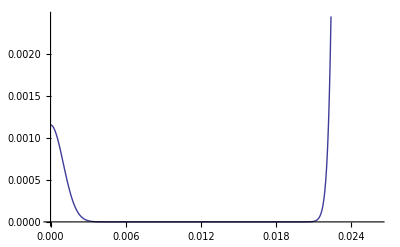

```mathematica
Plot[extremeSpectrum[x],{x,0,mostCongestedSpecWidth}]
```

Now, calculate the maximum scaled peak height

```mathematica
Maximize[{extremeSpectrum[x],0≤x≤mostCongestedSpecWidth},x]
```

Maximize::ztest1: Unable to decide whether numeric quantity -417339712683233 + 16000000000000000 Root[{-41610856053081745847660287316767 + 1595279999999999984000000000000000 Slot[« 1 »] + 921470400000000062400000000000 Power[« 2 »] Slot[« 1 »] &, « 185 »}] is equal to zero. Assuming it is.

{(ⅇ^(-1700902693188705775044915354384765625/(7397523242308154091360627955101456 Log[2])) (575919000000000039+997049999999999990000 ⅇ^(1700902693188705775044915354384765625/(7397523242308154091360627955101456 Log[2]))))/500000000000000000000,{x→417339712683233/16000000000000000}}

How different is the maximum scaled peak height from 1?

```mathematica
FullSimplify[1-(maxOrigHeight/extremeSpectrum[417339712683233/16000000000000000])]
```

1/(1+(997049999999999990000 ⅇ^(1700902693188705775044915354384765625/(7397523242308154091360627955101456 Log[2])))/575919000000000039)

It is approximately 1+5*10^-148

```mathematica
N[1/(1+(997049999999999990000 ⅇ^(1700902693188705775044915354384765625/(7397523242308154091360627955101456 Log[2])))/575919000000000039)]
```

4.99806×10^-148

Take the log base 2 to find out how many bits of precision would be needed:

```mathematica
N[Log[2,1/(1+(997049999999999990000 ⅇ^(1700902693188705775044915354384765625/(7397523242308154091360627955101456 Log[2])))/575919000000000039)]]
```

-489.324

We'd need at least a 490 bit number to represent the number as different than 1. Since double precision only gives us 53 bits, we're quite safe. And since this is the MOST different than 1 it could be (since this is the most congested spectrum) we are safe in calling it 1 in all congestions.

### Calculate max scaled height, taking sampling into consideration

#### Max height ≥ 1 (within 53 bits of precision)

The only way to get scaled heights less than 1 is to have the maximum sample be larger than the largest height. I can always arrange for the maximum amplitude peak to fall directly on a sample location and have the rest of the peaks be as far away and as small as possible. In a worst-case sampling, (which puts the rest of the peaks as close as possible to the middle peak), the sample location falls in the middle of the spectrum and there is only one sample. Then we get (using the above calculation about the 6 distant peaks, but with half the distance:

```mathematica
worstCaseSampledSpectrum[x_]:=6 glp[minOrigHeight,minHalfHeightWidth,0,x,0]+glp[maxOrigHeight,minHalfHeightWidth,0,x,mostCongestedSpecWidth/2]
```

```mathematica
N[FullSimplify[1-(maxOrigHeight/worstCaseSampledSpectrum[mostCongestedSpecWidth/2])]]
```

5.57101×10^-40

```mathematica
N[Log[2,FullSimplify[1-(maxOrigHeight/worstCaseSampledSpectrum[mostCongestedSpecWidth/2])]]]
```

-130.399

In this case only 131 bits are needed to express the difference from 1, but it is still a lot more than the 53 available at double precision.

#### Max height can be huge with a single sample.

In the above, I ignored the fact that I can move whichever peak I want under the sample. (I was still thinking like I did in the maximum of the spectrum analysis.) But really, I could easily put all the peaks as far away as possible from the single sample. Then the ratio of the height at that point to the height of the highest peak gives the largest scaled peak. This can easily be in the billions with the sample widths in my code.

```mathematica
reallyBigScaledHeightSpectrumWhenOneSampleInMiddle[x_]:=6 glp[minOrigHeight,minHalfHeightWidth,0,x,0]+glp[maxOrigHeight,minHalfHeightWidth,0,x,0]
```

```mathematica
N[FullSimplify[maxOrigHeight/reallyBigScaledHeightSpectrumWhenOneSampleInMiddle[mostCongestedSpecWidth/2]]]
```

1.03624×10^36

Yep, really big.

#### Making large heights when more samples, but only a single peak

The secret to making the heights large is arranging the peaks so that the largest sample is as small as possible.

In the experiment, we will set up a grid of equally-spaced sample points, then we want to know the maximum possible scaled height. The maximum possible scaled height comes when we minimize the largest sample. If we fix all the peak parameters but location, we can minimize the size of the largest sample by putting the peak halfway between it and the next sample. If we fix all parameters but width, we can minimize the size of the largest sample by decreasing the width. Height must be maximum because we want to maximize the ratio between the height and the largest sample. I'm not sure what to do about Lorentzianness.

When there is only one peak, we can (without loss of generality) put that peak at 0, half-way between two samples. Further, because of symmetry, we will only worry about samples on the non-negative side. The largest sample will be the first sample. The location of the first sample will be the sample spacing/2.

```mathematica
N[Map[Function[firstSampleLoc,Append[Maximize[{maxOrigHeight/glp[maxOrigHeight,minHalfHeightWidth,P,firstSampleLoc,0],0≤P≤1},{P},Reals],"firstSampleLoc"->firstSampleLoc]],{1/10,1/100,1/1000,1/10000,1/100000}]]
```

{{2.79809832272×10^2117,{P→0.},firstSampleLoc→0.1},{1.49441×10^21,{P→0.},firstSampleLoc→0.01},{2.3518,{P→1.},firstSampleLoc→0.001},{1.01352,{P→1.},firstSampleLoc→0.0001},{1.00014,{P→1.},firstSampleLoc→0.00001}}

Some quick experiments reveal that the optimum value of P will depend on the sample spacing. When the spacing is large, P appears to go toward 0 (for the light tails of the Gaussian). When it is small, P is optimized by 1 (for the steeper initial fall-off of the Lorentzian)

The same experiments indicate that the smaller the first sample is, the closer the ratio is to 1.

Using the same resolution used in the generated spectra, I arrive at:

```mathematica
glbioSamplesPerPPM=25/(453630122481774988/100000000000000000000)
```

625000000000000000000/113407530620443747

```mathematica
N[glbioSamplesPerPPM,20]
```

5511.0978660823826238

```mathematica
25/0.00453630122481774988
```

5511.0978660823826

```mathematica
N[Map[Function[firstSampleLoc,Append[Maximize[{maxOrigHeight/glp[maxOrigHeight,minHalfHeightWidth,P,firstSampleLoc,0],0≤P≤1},{P},Reals],"firstSampleLoc"->firstSampleLoc]],{1/glbioSamplesPerPPM}]]
```

{{1.04451,{P→1.},firstSampleLoc→0.000181452}}

#### Now, with two peaks

In the previous formula, the width of the spectrum did not come into play, only the sampling resolution. Now, when we look at two peaks, our main goal is to have the second peak have as little influence as possible on the sampled value (since the only influence it can have is to raise that value). To minimize the influence, we make it as small as possible, with as small tails as possible, and as far away as possible. Because "as far away as possible" means "at the other end of the spectrum", this adds an influence of spectrum width.

```mathematica
spectrumWidths={255535713894383631/100000000000000000,12143322568559618/10000000000000000,761733007296055642/1000000000000000000,530549597771693859/1000000000000000000,393124388410428127/1000000000000000000,298021719927547224/1000000000000000000,2280658974128357/10000000000000000,171535857174701128/1000000000000000000,121507450820750054/1000000000000000000,260837320427020625/10000000000000000000}
```

{255535713894383631/100000000000000000,6071661284279809/5000000000000000,380866503648027821/500000000000000000,530549597771693859/1000000000000000000,393124388410428127/1000000000000000000,37252714990943403/125000000000000000,2280658974128357/10000000000000000,21441982146837641/125000000000000000,60753725410375027/500000000000000000,417339712683233/16000000000000000}

```mathematica
N[spectrumWidths,18]
```

{2.55535713894383631,1.2143322568559618,0.761733007296055642,0.530549597771693859,0.393124388410428127,0.298021719927547224,0.2280658974128357,0.171535857174701128,0.121507450820750054,0.0260837320427020625}

```mathematica
Original spectrum widths:[2.55535713894383631,1.2143322568559618,0.761733007296055642,0.530549597771693859,0.393124388410428127,0.298021719927547224,0.2280658974128357,0.171535857174701128,0.121507450820750054,0.0260837320427020625]
```

```mathematica
twoPeakSpectrumRatio[P_,firstSampleLoc_,spectrumWidth_]:=maxOrigHeight/(glp[maxOrigHeight,minHalfHeightWidth,P,firstSampleLoc,0]+glp[minOrigHeight, minHalfHeightWidth, 0,firstSampleLoc,spectrumWidth])
```

Now, look at using two peaks and all the spectrum widths with the resolution from the GLBIO experiment:

```mathematica
N[Map[Function[spectrumWidth,Append[Maximize[{twoPeakSpectrumRatio[P,1/glbioSamplesPerPPM,spectrumWidth],0≤P≤1},{P},Reals],"spectrumWidth"->spectrumWidth]],spectrumWidths],20]
```

{{1.0445079319188184286,{P→1.},spectrumWidth→2.55535713894383631},{1.0445079319188184286,{P→1.},spectrumWidth→1.2143322568559618},{1.0445079319188184286,{P→1.},spectrumWidth→0.761733007296055642},{1.0445079319188184286,{P→1.},spectrumWidth→0.530549597771693859},{1.0445079319188184286,{P→1.},spectrumWidth→0.393124388410428127},{1.0445079319188184286,{P→1.},spectrumWidth→0.298021719927547224},{1.0445079319188184286,{P→1.},spectrumWidth→0.2280658974128357},{1.0445079319188184286,{P→1.},spectrumWidth→0.171535857174701128},{1.0445079319188184286,{P→1.},spectrumWidth→0.121507450820750054},{1.0445079319188184286,{P→1.},spectrumWidth→0.0260837320427020625}}

Technically, there is a dependence on spectrum width, but in this case it seems to make no practical difference.

If I set the spectrum width to the sample size, I can slightly affect the outcome (although, in this case, the assumption that putting the second peak at the spectrum width will put it as far away as possible from the first sample is false). Since the "spectrum width" variable is only used for the location of the second peak, I can set it to 0 (which is really the farthest away it can go from the sample if there is only one sample and it is located at the other end of the spectrum). In this case too, there is a small effect.

```mathematica
N[Map[Function[spectrumWidth,Append[Maximize[{twoPeakSpectrumRatio[P,1/glbioSamplesPerPPM,spectrumWidth],0≤P≤1},{P},Reals],"spectrumWidth"->spectrumWidth]],{1/glbioSamplesPerPPM,0}],20]
```

{{1.0444029116720319885,{P→1.},spectrumWidth→0.0001814520489927099952},{1.0444045839206921287,{P→1.},spectrumWidth→0}}

#### Seven peaks

The same logic for the second peak applies to all the other peaks. Thus, assuming the spectrum is large enough, we put them all on the opposite end of the spectrum from the main peak and make them identically small.

```mathematica
sixPeakSpectrumRatio[P_,firstSampleLoc_,spectrumWidth_]:=maxOrigHeight/(glp[maxOrigHeight,minHalfHeightWidth,P,firstSampleLoc,0]+6*glp[minOrigHeight, minHalfHeightWidth, 0,firstSampleLoc,spectrumWidth])
```

We can run this model (which is what we will actually use) on all spectrum widths

```mathematica
N[Map[Function[spectrumWidth,Append[Maximize[{sixPeakSpectrumRatio[P,1/glbioSamplesPerPPM,spectrumWidth],0≤P≤1},{P},Reals],"spectrumWidth"->spectrumWidth]],spectrumWidths],30]
```

{{1.0445079319188184285691427848,{P→1.},spectrumWidth→2.55535713894383631},{1.0445079319188184285691427848,{P→1.},spectrumWidth→1.2143322568559618},{1.0445079319188184285691427848,{P→1.},spectrumWidth→0.761733007296055642},{1.0445079319188184285691427848,{P→1.},spectrumWidth→0.530549597771693859},{1.0445079319188184285691427848,{P→1.},spectrumWidth→0.393124388410428127},{1.0445079319188184285691427848,{P→1.},spectrumWidth→0.298021719927547224},{1.0445079319188184285691427848,{P→1.},spectrumWidth→0.2280658974128357},{1.0445079319188184285691427848,{P→1.},spectrumWidth→0.171535857174701128},{1.0445079319188184285691427848,{P→1.},spectrumWidth→0.121507450820750054},{1.0445079319188184285691427848,{P→1.},spectrumWidth→0.0260837320427020625}}

Again, spectrum width had no detectable effect out to 30 decimal places.

The exact maximum height for the largest spectrum (which will be the upper bound for all the heights) is:

```mathematica
Map[Function[spectrumWidth,Append[Maximize[{sixPeakSpectrumRatio[P,1/glbioSamplesPerPPM,spectrumWidth],0≤P≤1},{P},Reals],"spectrumWidth"->spectrumWidth]],{Max[spectrumWidths]}]
```

{{99704999999999999/(50000000000000000 (46098128429645906017599260497202286194960752806159/24146161572327132422492383415004050720000000000000+(575919000000000039 ⅇ^(-2550360465194740553051052326193418163500009/(1155863006610649076775098117984602500 Log[2])))/500000000000000000000)),{P→1},spectrumWidth→255535713894383631/100000000000000000}}

```mathematica
maxScaledHeight=FullSimplify[99704999999999999/(50000000000000000 (46098128429645906017599260497202286194960752806159/24146161572327132422492383415004050720000000000000+(575919000000000039 ⅇ^(-2550360465194740553051052326193418163500009/(1155863006610649076775098117984602500 Log[2])))/500000000000000000000))]
```

1/(288965751652662269193774529496150625/301827019654089155281154792687550634+(575919000000000039 ⅇ^(-2550360465194740553051052326193418163500009/(1155863006610649076775098117984602500 Log[2])))/997049999999999990000)

### Recalculate new maximum area using the correct maximum height

```mathematica
Minimize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤maxScaledHeight,minHalfHeightWidth≤G≤maxHalfHeightWidth},{M,G,P}]
```

{(133156274490846315260057442353883 √(π/Log[2]))/9649025784677419258075000000000000000000,{M→191973000000000013/11964791972999999880013,G→21502213900997721/12500000000000000000,P→0}}

```mathematica
N[Minimize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤maxScaledHeight,minHalfHeightWidth≤G≤maxHalfHeightWidth},{M,G,P}],20]
```

{2.937922766273879908×10^-8,{M→0.000016044825554277107775,G→0.00172017711207981768,P→0}}

```mathematica
Maximize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤maxScaledHeight,minHalfHeightWidth≤G≤maxHalfHeightWidth},{M,G,P}]
```

{(112387630707607971 π)/(5000000000000000000 (288965751652662269193774529496150625/301827019654089155281154792687550634+(575919000000000039 ⅇ^(-2550360465194740553051052326193418163500009/(1155863006610649076775098117984602500 Log[2])))/997049999999999990000)),{M→1/(288965751652662269193774529496150625/301827019654089155281154792687550634+(575919000000000039 ⅇ^(-2550360465194740553051052326193418163500009/(1155863006610649076775098117984602500 Log[2])))/997049999999999990000),G→112387630707607971/2500000000000000000,P→1}}

```mathematica
N[FullSimplify[Maximize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤maxScaledHeight,minHalfHeightWidth≤G≤maxHalfHeightWidth},{M,G,P}]],20]
```

{0.073758168890726301241,{M→1.0445079319188184286,G→0.0449550522830431884,P→1.}}